### Omega Plots

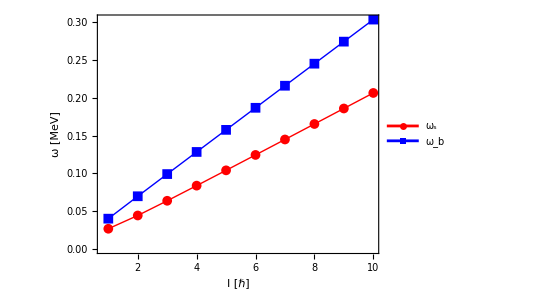

```mathematica
omegab={0.04000,0.06964,0.09899,0.12825,0.15746,0.18665,0.21583,0.24500,0.27416,0.30332};
omegas={0.02667,0.04421,0.06366,0.08368,0.10393,0.12430,0.14474,0.16523,0.18574,0.20628};
ListPlot[{omegas,omegab}, Joined->{True, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False, FrameStyle->Directive[Black, Thick],PlotStyle->{{Red, Thick},{Blue,Thick}}, PlotRange->Full,FrameLabel->{"I [ℏ]","ω [MeV]"},LabelStyle->{17, Black, Bold,FontFamily->"Arial"},PlotLegends->Placed[{"ω_s","ω_b"},{0.2,0.8}],AspectRatio->0.75]
```

### Energy 1

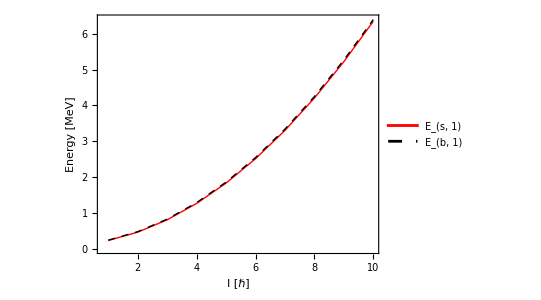

```mathematica
en1s={0.23629,0.46803,0.81219,1.26812,1.83564,2.51471,3.30529,4.20737,5.22095,6.34602};
en1b={0.24296,0.48074,0.82985,1.29040,1.86241,2.54589,3.34083,4.24726,5.26516,6.39454};
ListPlot[{en1s,en1b}, Joined->{True, True},PlotMarkers->None,Frame->True,Axes->False, FrameStyle->Directive[Black, Thick],PlotStyle->{{Red, Thick},{Black,Dashed,Thick}}, PlotRange->Full,FrameLabel->{"I [ℏ]","Energy [MeV]"},LabelStyle->{17, Black, Bold,FontFamily->"Arial"},PlotLegends->Placed[{"E_(s, 1)","E_(b, 1)"},{0.2,0.8}],AspectRatio->0.75]
```